## Distribucion Truncada

```mathematica
𝒟=TruncatedDistribution[{-∞,0.5},𝒹=CauchyDistribution[0,1]];
```

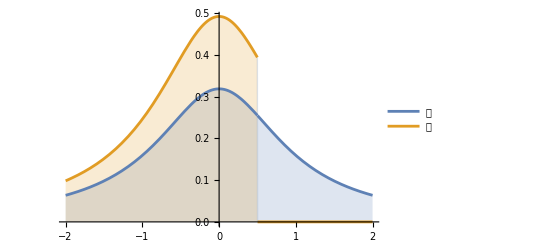

```mathematica
Plot[{Legended[PDF[𝒹,x],"𝒹"],Legended[PDF[𝒟,x],"𝒟"]},{x,-2,2},Filling->Axis]
```

```mathematica
dtrun=PDF[CauchyDistribution[0,1],x]
```

1/(π (1+x^2))

```mathematica
dtrun2=ProbabilityDistribution[1/(π (1+x^2)),{x,-Infinity,0.5}]
```

ProbabilityDistribution[1/((1+x^2) π),{x,-∞,0.5}]

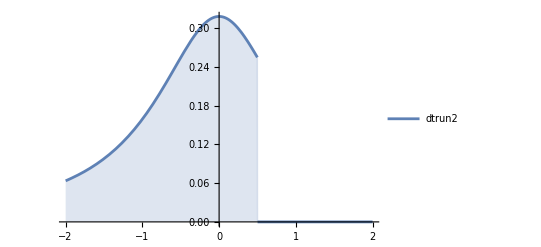

```mathematica
Plot[Legended[PDF[dtrun2,x],"dtrun2"],{x,-2,2},Filling->Axis]
```

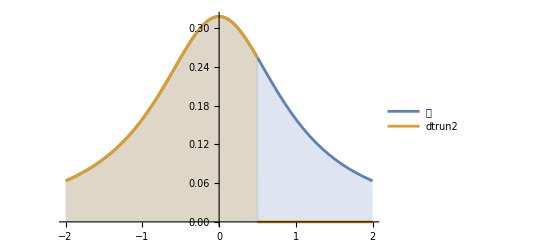

```mathematica
Plot[{Legended[PDF[𝒹,x],"𝒹"],Legended[PDF[dtrun2,x],"dtrun2"]},{x,-2,2},Filling->Axis]
```

```mathematica
cte=NIntegrate[PDF[dtrun2,x],{x,-10000000,.5}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.617059}. NIntegrate obtained 0.647584 and 4.11408×10^-6 for the integral and error estimates.

0.647584

```mathematica
dtrun3=ProbabilityDistribution[(1/cte)/(π (1+x^2)),{x,-Infinity,0.5}]
```

ProbabilityDistribution[0.491535/(1+x^2),{x,-∞,0.5}]

```mathematica
NIntegrate[PDF[dtrun3,x],{x,-10000000,.5}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-0.617059}. NIntegrate obtained 1. and 6.35297×10^-6 for the integral and error estimates.

1.

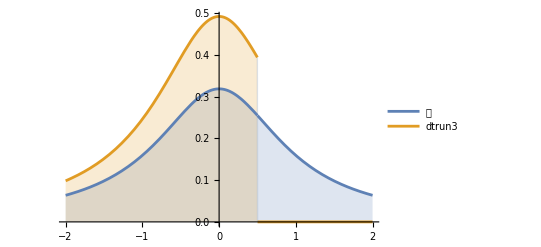

```mathematica
Plot[{Legended[PDF[𝒹,x],"𝒹"],Legended[PDF[dtrun3,x],"dtrun3"]},{x,-2,2},Filling->Axis]
```

### Ejercicio :

Ejercicio : El diámetro de un arándano se describe por una distribución normal con media de 16 mm y desviación estándar de 1, 6 mm. Un arándano debe tener al menos 15 mm de diametro para venderse entero; de lo contrario, se utiliza en la elaboración de jugo de arándanos . 
a) Encuentre la distribución del tamaño  de los arándanos que se venden enteros.
b) ¿Cual es su promedio, mediana y moda?

```mathematica
disA=NormalDistribution[16,1.6]
```

NormalDistribution[16,1.6]

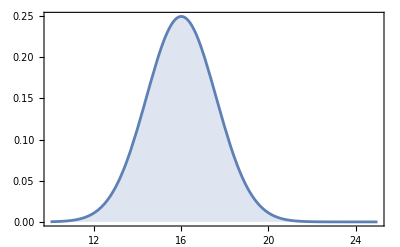

```mathematica
grdisA=Plot[PDF[disA,x],{x,10,25},PlotRange->All,Frame->True,Filling->Bottom]
```

```mathematica
distVA=TruncatedDistribution[{15,∞},disA]
```

TruncatedDistribution[{15,∞},NormalDistribution[16,1.6]]

```mathematica
distVAconst=NIntegrate[PDF[disA,x],{x,15,∞}]
```

0.734014

```mathematica
distVAmanual=ProbabilityDistribution[(1/distVAconst) PDF[disA,x],{x,15,∞}]
```

ProbabilityDistribution[0.339692 ⅇ^(-0.195313 (-16+x)^2),{x,15,∞}]

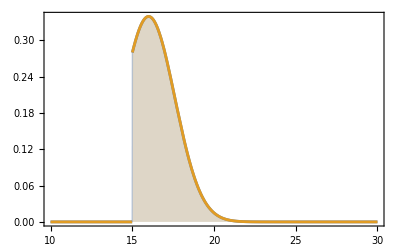

```mathematica
Plot[{PDF[distVAmanual,x],PDF[distVA,x]},{x,10,30},Filling->Bottom,Frame->True,PlotRange->All]
```

```mathematica
Mean[distVA]
```

16.7153

```mathematica
Mean[distVAmanual]
```

16.7153

```mathematica
Median[distVAmanual]
```

16.5437

```mathematica
FindRoot[D[PDF[distVA,x],x]==0,{x,17.}]
```

{x→16.}

¿Cual es la Probabilidad de vender arandanos con un diametro mayor a 18 mm?

```mathematica
Probability[x>=18, x\[Distributed]distVA]
```

0.143934

```mathematica
NIntegrate[PDF[distVA,x], {x,18., ∞}]
```

0.143934

### Ejemplo2

```mathematica
Nombres=StarData[EntityClass["Star",{EntityProperty["Star","DistanceFromEarth"]->TakeSmallest[1000]}]];
```

Distances:

```mathematica
datastars=StarData[Nombres,"Mass"];
```

```mathematica
datMasa=Select[datastars,NumberQ[#[[1]]]&][[All,1]]/StarData["Sun","Mass"][[1]];
```

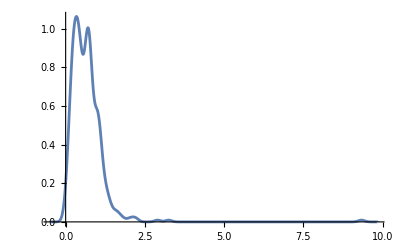

```mathematica
SmoothHistogram[datMasa]
```

y uds. continuen con los datos de planetas...y comparen su hay un “gap” entre ambas distribuciones.

## Condicional

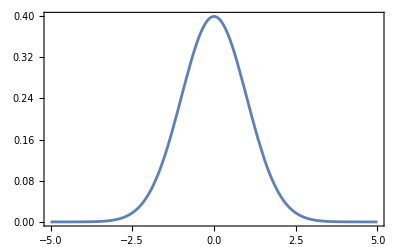

```mathematica
Plot[PDF[NormalDistribution[],x],{x,-5,5},Frame->True]
```

```mathematica
Probability[x>0,x\[Distributed]NormalDistribution[]]
```

1/2

```mathematica
Probability[x>2,x\[Distributed]NormalDistribution[]]//N
```

0.0227501

```mathematica
Probability[x>2 \[Conditioned] x>0,x\[Distributed]NormalDistribution[]]
```

1-Erf[√2]

```mathematica
%//N
```

0.0455003

```mathematica
Probability[x>=18 \[Conditioned] x>=15,x\[Distributed]NormalDistribution[16,1.6]]
```

0.143934

```mathematica
PDF[TruncatedDistribution[{2,∞},NormalDistribution[]],x]
```

Piecewise[{{(ⅇ^(-x^2/2))/(√(2 π) (1-1/2 Erfc[-√2])), x>2}, {0, True}}]

```mathematica
PDF[TruncatedDistribution[{2,∞},NormalDistribution[]],x][[1,1,1]]
```

(ⅇ^(-x^2/2))/(√(2 π) (1-1/2 Erfc[-√2]))

```mathematica
Integrate[PDF[TruncatedDistribution[{0,∞},NormalDistribution[]],x],{x,2,∞}]
```

Erfc[√2]

```mathematica
N@%
```

0.0455003

```mathematica
Probability[x<X \[Conditioned] x>-2,x\[Distributed]NormalDistribution[]]
```

Piecewise[{{(Erf[√2]+Erf[X/(√2)])/(1+Erf[√2]), X>-2}, {0, True}}]

## Multivariate Distributions

### Ejemplo distribucion multivariada continua

```mathematica
f=Exp[- (1+x)/y] x/y^4;
```

```mathematica
Integrate[f,x,y]
```

-(ⅇ^(-(1+x)/y) (x+x^2+y+2 x y))/((1+x)^2 y)

```mathematica
Integrate[f,{x,0,∞},{y,0,∞}]
```

1

```mathematica
Plot3D[f,{x,0,5},{y,0,2},PlotRange->All,AxesLabel->{"x","y"}]
```

General::munfl: Exp[-6995.51] is too small to represent as a normalized machine number; precision may be lost.

-Graphics3D-

```mathematica
Plot3D[f,{x,0,2},{y,0,2},PlotRange->All,AxesLabel->{"x","y"}]
```

General::munfl: Exp[-6994.01] is too small to represent as a normalized machine number; precision may be lost.

-Graphics3D-

General::munfl: Exp[-7001.] is too small to represent as a normalized machine number; precision may be lost.

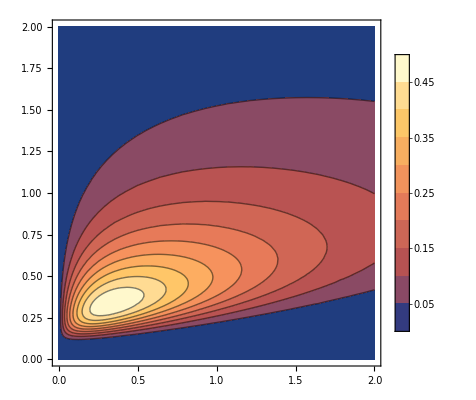

```mathematica
ContourPlot[f,{x,0,2},{y,0,2},PlotLegends->Automatic]
```

### Probabilidad

```mathematica
f=Exp[- (1+x)/y] x/y^4;
```

```mathematica
pdff=ProbabilityDistribution[f,{x,0,∞},{y,0,∞}]
```

ProbabilityDistribution[(x1 ⅇ^(-(1+x1)/x2))/x2^4,{x1,0,∞},{x2,0,∞}]

```mathematica
cdff=CDF[pdff,{x,y}]
```

Piecewise[{{(ⅇ^(-(1+x)/y) ((-1+ⅇ^(x/y)) y+x^2 (-1+ⅇ^(x/y) y)+x (-1+2 (-1+ⅇ^(x/y)) y)))/((1+x)^2 y), x>0&&y>0}, {0, True}}]

```mathematica
PDF[pdff,{x,y}]
```

Piecewise[{{(ⅇ^(-(1+x)/y) x)/y^4, x>0&&y>0}, {0, True}}]

```mathematica
Plot3D[cdff,{x,0,50},{y,0,50},PlotRange->All]
```

-Graphics3D-

```mathematica
marginalfx=Integrate[Exp[- (1+x)/y] x/y^4,{y,0,∞},Assumptions->x>0]
```

(2 x)/(1+x)^3

```mathematica
marginalfy=Integrate[Exp[- (1+x)/y] x/y^4,{x,0,∞},Assumptions->y>0]
```

ⅇ^(-1/y)/y^2

```mathematica
pdffx=PDF[MarginalDistribution[pdff,1],x]
```

Piecewise[{{(2 x)/(1+x)^3, x>0}, {0, True}}]

```mathematica
pdffx=PDF[MarginalDistribution[pdff,2],y]
```

Piecewise[{{ⅇ^(-1/y)/y^2, y>0}, {0, True}}]

### Marginal Distributions 1

```mathematica
PDF[BinormalDistribution[ρ],{x,y}]
```

(ⅇ^((-x^2-y^2+2 x y ρ)/(2 (1-ρ^2))))/(2 π √(1-ρ^2))

```mathematica
Mean[BinormalDistribution[ρ]]
```

{0,0}

```mathematica
MarginalDistribution[BinormalDistribution[ρ],1]
```

NormalDistribution[0,1]

```mathematica
PDF[%,x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
Integrate[(ⅇ^((-x^2-y^2+2 x y ρ)/(2 (1-ρ^2))))/(2 π √(1-ρ^2)),{y,-∞,∞},Assumptions->-1<ρ<1&&Element[ρ,Reals]]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
MarginalDistribution[BinormalDistribution[ρ],2]
```

NormalDistribution[0,1]

```mathematica
PDF[%,y]
```

(ⅇ^(-y^2/2))/(√(2 π))

```mathematica
Manipulate[Plot3D[PDF[BinormalDistribution[ρ],{x,y}],{x,-5,5},{y,-5,5},PlotRange->All,PlotPoints->50],{{ρ,0},-1,1.,.1}]
```

```mathematica
Manipulate[ContourPlot[PDF[BinormalDistribution[ρ],{x,y}],{x,-5,5},{y,-5,5},PlotRange->All,PlotPoints->50],{{ρ,0},-1,1.,.1}]
```

```mathematica
𝒟=ProbabilityDistribution[6( x-y/2)^2,{x,0,1},{y,0,1}];
```

```mathematica
NIntegrate[6( x-y/2)^2,{x,0,1},{y,0,1}]
```

1.

```mathematica
ℳ1=MarginalDistribution[𝒟,1]
```

MarginalDistribution[ProbabilityDistribution[6 (x1-x2/2)^2,{x1,0,1},{x2,0,1}],1]

```mathematica
ℳ2=MarginalDistribution[𝒟,2]
```

MarginalDistribution[ProbabilityDistribution[6 (x1-x2/2)^2,{x1,0,1},{x2,0,1}],2]

```mathematica
PDF[ℳ1,z]
```

Piecewise[{{1/2 (1-6 z+12 z^2), 0<z<1}, {0, True}}]

```mathematica
PDF[ℳ2,z]
```

Piecewise[{{1/2 (4-6 z+3 z^2), 0<z<1}, {0, True}}]

```mathematica
{{Mean[ℳ1],Mean[ℳ2]},Mean[𝒟]}
```

{{3/4,3/8},{3/4,3/8}}

### Marginal Distributions 2

```mathematica
PDF[BinormalDistribution[{Subscript[μ, 1],Subscript[μ, 2]},{Subscript[σ, 1],Subscript[σ, 2]},ρ],{x,y}]
```

(ⅇ^((-(x-μ_1)^2/σ_1^2-(y-μ_2)^2/σ_2^2+(2 ρ (x-μ_1) (y-μ_2))/(σ_1 σ_2))/(2 (1-ρ^2))))/(2 π √(1-ρ^2) σ_1 σ_2)

```mathematica
TraditionalForm@%
```

(exp((-(x-μ_1)^2/σ_1^2+(2 ρ (x-μ_1) (y-μ_2))/(σ_1 σ_2)-(y-μ_2)^2/σ_2^2)/(2 (1-ρ^2))))/(2 π √(1-ρ^2) σ_1 σ_2)

```mathematica
PDF[MarginalDistribution[BinormalDistribution[{Subscript[μ, 1],Subscript[μ, 2]},{Subscript[σ, 1],Subscript[σ, 2]},ρ],1],x]
```

(ⅇ^(-(x-μ_1)^2/(2 σ_1^2)))/(√(2 π) σ_1)

```mathematica
PDF[MarginalDistribution[BinormalDistribution[{Subscript[μ, 1],Subscript[μ, 2]},{Subscript[σ, 1],Subscript[σ, 2]},ρ],2],y]
```

(ⅇ^(-(y-μ_2)^2/(2 σ_2^2)))/(√(2 π) σ_2)

```mathematica
Manipulate[Plot3D[PDF[BinormalDistribution[{μ1,μ2},{σ1,σ2},ρ],{x,y}],{x,-5,5},{y, -5,5},PlotRange->All,PlotPoints->50],{{ρ,0},-1,1.,.05},{{μ1,0},-1.,1.,.1},{{μ2,0},-1.,1.,.1},{{σ1,.5},.1,1.,.1},{{σ2,.5},.1,1.,.1}]
```

BinormalDistribution::corprm: Parameter 1. at position 3 in BinormalDistribution[{0,0},{0.5,0.5},1.] is expected to be greater than -1 and less than 1.

BinormalDistribution::corprm: Parameter 1. at position 3 in BinormalDistribution[{0.,0.},{0.5,0.5},1.] is expected to be greater than -1 and less than 1.

BinormalDistribution::corprm: Parameter 1. at position 3 in BinormalDistribution[{0,0},{0.5,0.5},1.] is expected to be greater than -1 and less than 1.

General::stop: Further output of BinormalDistribution::corprm will be suppressed during this calculation.

## BootStrap

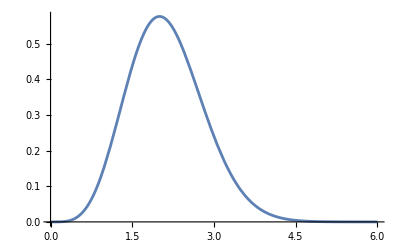

```mathematica
distOrig=Plot[PDF[ChiDistribution[5],x],{x,0,6}]
```

```mathematica
datos=RandomVariate[ChiDistribution[5],100];
```

```mathematica
Length@datos
```

100

```mathematica
dists=FindDistribution[datos,5]
```

{NormalDistribution[2.17703,0.730806],WeibullDistribution[3.2461,2.43048],GammaDistribution[8.20147,0.265444],MixtureDistribution[{0.445538,0.554462},{NormalDistribution[1.68103,0.482588],NormalDistribution[2.57558,0.647735]}],ChiDistribution[5.14613]}

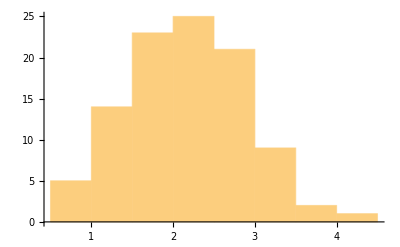

```mathematica
Histogram[datos]
```

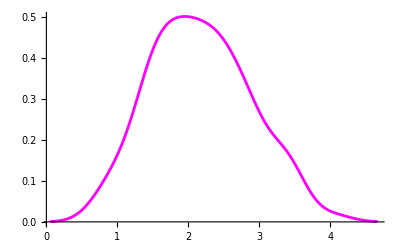

```mathematica
kdedatos=SmoothHistogram[datos,PlotStyle->Magenta]
```

```mathematica
masdatos=RandomChoice[datos,{1000,100}];
```

```mathematica
Dimensions[masdatos]
```

{1000,100}

```mathematica
AbsoluteTiming[sols=FindMaximum[LogLikelihood[NormalDistribution[μ,σ],#],{{μ,2.05},{σ,.71}},Method->"Newton"]& /@ masdatos;//Quiet]
```

{1.72602,Null}

```mathematica
sols[[1;;10]]//TableForm
```

-99.8775 | μ→2.18124
σ→0.65694
-110.116 | μ→2.09297
σ→0.727764
-102.279 | μ→2.08184
σ→0.672905
-103.132 | μ→2.18614
σ→0.678669
-104.478 | μ→2.08775
σ→0.687867
-104.963 | μ→2.15113
σ→0.69121
-121.553 | μ→2.16826
σ→0.815942
-113.878 | μ→2.13398
σ→0.755666
-118.759 | μ→2.14876
σ→0.79346
-96.697 | μ→2.13917
σ→0.636374

```mathematica
sols[[1;;5,2]]
```

{{μ→2.18124,σ→0.65694},{μ→2.09297,σ→0.727764},{μ→2.08184,σ→0.672905},{μ→2.18614,σ→0.678669},{μ→2.08775,σ→0.687867}}

```mathematica
mues=μ/.sols[[All,2]];
```

```mathematica
Length@mues
```

1000

```mathematica
sigs=σ/.sols[[All,2]];
```

```mathematica
Length@sigs
```

1000

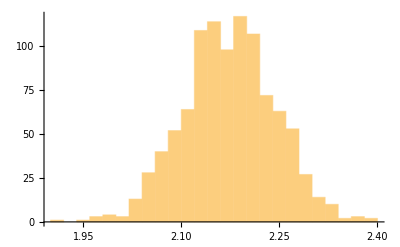

```mathematica
Histogram@mues
```

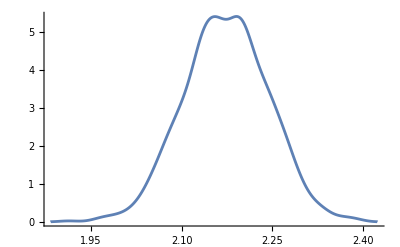

```mathematica
SmoothHistogram[mues,PlotRange->All]
```

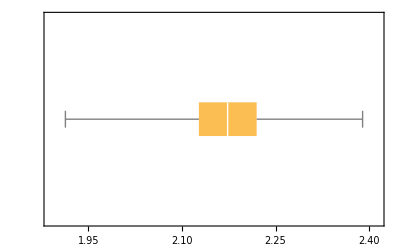

```mathematica
BoxWhiskerChart[mues,BarOrigin->Left]
```

```mathematica
Mean[mues]
```

2.1733

```mathematica
StandardDeviation[mues]
```

0.0699041

```mathematica
Quantile[mues,{0.025,0.975}]
```

{2.0389,2.30472}

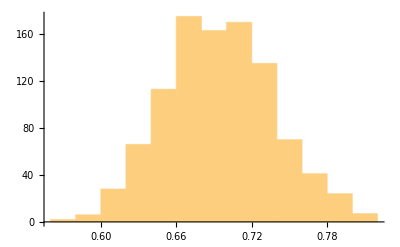

```mathematica
Histogram@sigs
```

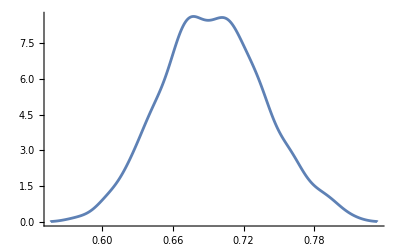

```mathematica
SmoothHistogram[sigs,PlotRange->All]
```

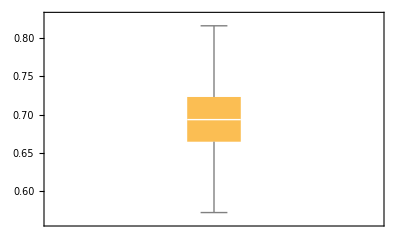

```mathematica
BoxWhiskerChart[sigs]
```

```mathematica
Mean[sigs]
```

0.694223

```mathematica
StandardDeviation[sigs]
```

0.0432167

```mathematica
Quantile[sigs,{0.025,0.975}]
```

{0.610666,0.783398}

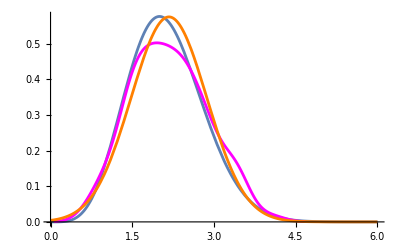

```mathematica
Show[distOrig,kdedatos,Plot[PDF[NormalDistribution[Mean[mues],Mean[sigs]],x],{x,0,6},PlotStyle->Orange]]
```

## Metodo Momentos

```mathematica
Moment[NormalDistribution[μ,σ],#]&/@Range[5]//TableForm
```

μ
μ^2+σ^2
μ (μ^2+3 σ^2)
μ^4+6 μ^2 σ^2+3 σ^4
μ (μ^4+10 μ^2 σ^2+15 σ^4)

```mathematica
datos=RandomVariate[NormalDistribution[4.2,0.53],100];
```

```mathematica
datosM1=Moment[datos,1]
```

4.29548

```mathematica
datosM2=Moment[datos,2]
```

18.7483

```mathematica
datosT1=Moment[NormalDistribution[μ,σ],1]
```

μ

```mathematica
datosT2=Moment[NormalDistribution[μ,σ],2]
```

μ^2+σ^2

```mathematica
sol=Solve[{datosM1==datosT1, datosM2==datosT2},{μ,σ}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{μ→4.29548,σ→-0.545064},{μ→4.29548,σ→0.545064}}

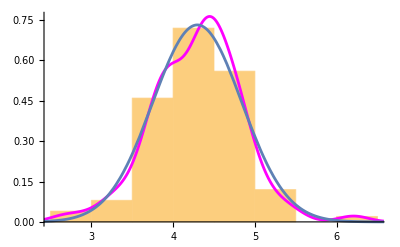

```mathematica
Show[Histogram[datos,Automatic,"PDF"],SmoothHistogram[datos,PlotStyle->Magenta],Plot[PDF[NormalDistribution[μ,σ]/.sol[[2]],x],{x,0,8}]]
```